```mathematica
Manipulate[
Module[
{K0,KK,X,p1,p2,p3,p4,d,n},

X={-1.6252,-1.46445,-0.8421,-0.695,-0.5113,-0.43,-0.1,-0.44,0.07542,0.261,0.269,0.325,0.471,0.47598,0.6486,0.811,1.0982,1.48,1.4865,1.561};
n=Length[X];
K0[u_]:=If[Abs[u]≤1,3/4(1-u^2),0];
KK[u_]:=1/h K0[u/h];
(*
K0[u_]:=1/Sqrt[2 Pi]Exp[-(1/2)u^2];
KK[u_]:=1/h K0[u/h];
*)
d[x_]:=1/n Sum[KK[x-xx],{xx,X}];

p1=Histogram[X,{0.5},"PDF",Axes->False];
p2=Plot[KK[xx-x],{xx,-5,5},PlotRange->{Automatic,{0,0.75}}, PlotStyle->Darker[Blue]];
p3=Plot[d[x],{x,-5,5},PlotStyle->Directive[Red,Thick], Exclusions->None];

p4=Graphics[
{
Black,
Line[{{-5,0},{5,0}}],
Darker[Green],
Table[Line[{{xx,0},{xx,KK[x-xx]}}],{xx,X}],
Thick,Red,
Line[{{x,0},{x,d[x]}}],
Black,
Table[Disk[{xx,0},Scaled[{0.007,0.01}]],{xx,X}]
}
];

Show[{p1,p2,p4,p3},PlotRange->{{-4,4},{0,0.75}},ImageSize->600]
]
,
{{h,1},0.25,2},
{{x,-1.75},-4,4}
]
```

1

1

1.

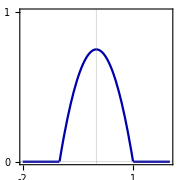

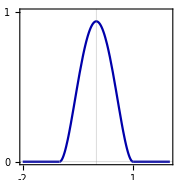

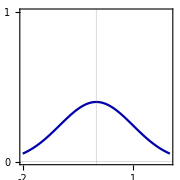

```mathematica
K1[u_]:=If[Abs[u]≤1,3/4(1-u^2),0]
K2[u_]:=If[Abs[u]≤1,15/16(1-u^2)^2,0]
K3[u_]:=1/Sqrt[2 Pi]Exp[-(1/2)u^2]

Integrate[K1[u],{u,-10,10}]
Integrate[K2[u],{u,-10,10}]
Integrate[K3[u],{u,-10,10}]//N

doit[k_]:=Plot[k[u],{u,-2,2},PlotTheme->"Scientific",PlotRange->{Automatic, {0,1}},AspectRatio->1,FrameTicks->{{{0,1},None},{{-2,-1,0,1,2},None}},ImageSize->Small, PlotStyle->Darker[Blue]]

doit[K1]
Export[NotebookDirectory[]<>"k1.pdf",%];
doit[K2]
Export[NotebookDirectory[]<>"k2.pdf",%];
doit[K3]
Export[NotebookDirectory[]<>"k3.pdf",%];
```